# Estadística

## Distribución binomial

Es una distribución de probabilidad discreta que describe la probabilidad de un número sucesivo de eventos en un experimento donde el resultado es binario (éxito o fracaso), donde la probabilidad de éxito está dada por p, y la probabilidad de fracaso es q = 1-p. Su función de probabilidad es

f(k, n, p) = (n
k) p^k (1-p)^(n-k),
donde n es el número de intentos, y k es el número de éxitos.
El valor esperado es

E(X) = nP,

y la varianza

V(X) = E(X^2) = nPQ.

Ejemplo

Se hace un experimento en el cual se hace 100 tiros sucesivos de una moneda y se mide el número de veces que sale una cierta cara. El número de intentos es n=100, la probabilidad de éxito es p = 0.5. Si se grafica la probabilidad de obtener cada número de exitos se obtiene una distribución como la que se muestra.

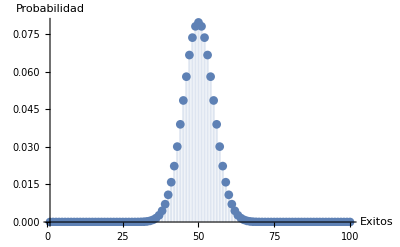

```mathematica
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,100},PlotRange->All,PlotMarkers->Automatic, AxesLabel->{"Exitos", "Probabilidad"}]
```

## Distribución de Poisson

## Teorema del límite central

La media aritmética de la suma de un gran número de variables aleatorias independientes se distribuye aproximadamente en una distribución normal sin importar sus distribuciones individuales.

```mathematica
(* Fuente: http://www.demonstrations.wolfram.com/TheCentralLimitTheorem/ *)
Manipulate[SeedRandom[seed];
Show[Histogram[Table[Mean[RandomReal[{0,100},n]],{200}],{35,65,1}],Plot[200*PDF[NormalDistribution[50,Sqrt[9999/(12 n)]],x],{x,35,65}],ImageSize->{500,300}],{{n,20,"Tamaño de la muestra"},10,200,1,Appearance->"Labeled"},{{seed,1,"Semilla"},1,100000,1}]
```

## Distribución normal

La importancia de esta distribución radica en que permite modelar numerosos fenómenos naturales, sociales y psicológicos. Mientras que los mecanismos que subyacen a gran parte de este tipo de fenómenos son desconocidos, por la enorme cantidad de variables incontrolables que en ellos intervienen, el uso del modelo normal puede justificarse asumiendo que cada observación se obtiene como la suma de unas pocas causas independientes (Fuente: Wikipedia). Su función de densidad de probabilidad es
f(x) = 1/(σ √(2 π))e^(-(x-μ)^2/(2 σ^2)).

Ejemplo

El coeficiente intelectual se distribuye aproximadamente de forma normal con media 100 y desviación estándar 16. ¿Cuál es la probabilidad de que un individuo tenga un IQ a) menor a 90, b) mayor a 130 y c) entre 95 y 105?

```mathematica
μ = 100;
σ = 16;
Print["a) " <>ToString[100*N[∫_(-∞)^90 PDF[NormalDistribution[μ,σ],x]ⅆx]] <> " %"]
Print["b) " <>ToString[100*N[∫_130^∞ PDF[NormalDistribution[μ,σ],x]ⅆx]] <> " %"]
Print["c) " <>ToString[100*N[∫_95^105 PDF[NormalDistribution[μ,σ],x]ⅆx]] <> " %"]
```

a) 26.5986 %

b) 3.03964 %

c) 24.5339 %

a) ¿Cuál es la probabilidad que la media del IQ de un grupo de 12 personas escogido aleatoriamente esté entre 95 y 105? b) ¿Qué tan grande debe ser la muestra para tener una probabilidad de 95 % de que la media del IQ esté entre estos límites?

Supongamos que se hace una serie de n observaciones, x_1, x_2,...,x_n , sobre una variable aleatoria y se calcula su media x̄, se se realiza otra serie de n onservaciones  x'_1, x'_2,...,x'_n  y se calcula su media x̄', si se sigue el procedimiendo sucesivamente se obtendrá una distribución de las medias. A esta distribución se le conoce como distribución de muestreo. Para averiguar cómo son los valores de expectación de esta distribución se hace

E(n x̄) = E(x_1+ x_2+...+x_n ) = E(x_1) + E(x_2) + ... + E(x_n)  = n μ,
V(n x̄) = V(x_1+ x_2+...+x_n ) = V(x_1) + V(x_2) + ... + V(x_n)  = n σ^2.

Con esto se puede calcular E y V sobre x̄.

E(x̄) = E((n x̄)/n) = (E(n x̄))/n = μ,
V(x̄) = V((n x̄)/n) = (V(n x̄))/n^2 = σ^2/n.

La distribución de la muestra es una distribución normal con media μ y varianza σ^2/n. Entonces

```mathematica
μ = 100;
σ = 16;
n = 12;
Print["a) " <>ToString[100*N[∫_95^105 PDF[NormalDistribution[μ,√(σ^2/n)],x]ⅆx]] <> " %"]
Clear[n];
Off[Solve::ifun];
Print["b) n = " <>ToString[Ceiling[n /. Solve[∫_95^105 PDF[NormalDistribution[μ,√(σ^2/n)],x]ⅆx == 0.95,n][[1]]]]]
```

a) 72.0984 %

b) n = 40

Se puede obtener una aproximación numérica a esta solución generando la distribución de las medias e integrando de 95 a 105.

```mathematica
Manipulate[
SeedRandom[seed];
μ =100;
σ = 16;
n = 12; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
m = Mean[sample];
AppendTo[dist,m];,
{k}
];
Show[
Histogram[dist,20,"ProbabilityDensity",PlotLabel->"P = " <> ToString[100*Integrate[PDF[HistogramDistribution[dist],x],{x,95,105}]]<> " %"],
Plot[Evaluate[PDF[NormalDistribution[μ,√(σ^2/n)],x]],{x,0,200},PlotRange->Full]
]
,
{{k,100},1,2450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

## Distribución χ^2

La distribución χ^2 con k grados de libertad es la distribución de la suma de los cuadrados de k variables normales independientes Y = Z_1^2+Z_2^2+ ... + Z_k^2, donde cada Z es independiente y está normalmente distribuido con media cero y varianza uno. La distribución χ^2 se puede interpretar como la distribución del cuadrado de la desviación estándar en una muestra. En concreto (n-1) S^2/σ^2 sigue la distribución χ^2.

```mathematica
Manipulate[
SeedRandom[seed];
data= RandomVariate[NormalDistribution[0,1],10^4]^2;
Do[
data += RandomVariate[NormalDistribution[0,1],10^4]^2;,
{k-1}
];
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[Evaluate[PDF[ChiSquareDistribution[k],x]],{x,0,100},PlotRange->Full]
],
{{k,2},1,50,1,Appearance->"Labeled"},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

Ejemplo

El coficiente intelectual es aproximadamente normalmente distribuido con μ=100, y σ = 16. En un grupo de 10 individuos seleccionados aleatoriamente, ¿cuál es la probabilidad de que la desviación estándar observada ‘s’ sea menor a 8.8?

En una muestra con n grados de libertad la distribución de su varianza está relacionada con la distribución χ^2, (n-1) S^2/σ^2 sigue la distribución χ^2. Sea f(x) la función de densidad de la distribución χ^2, con esto se puede obtener la probabilidad de que la desviación estándar sea menor a 8.8 integrando con los límites x_i = 0, x_f = (n-1) 8.8/σ^2, de manera que ∫_x_i^x_f f(x) dx = 0.0257108. A continuación se hará la prueba generando la distribución (n-1) S^2/σ^2 y comparando con la distribución χ^2.

```mathematica
Manipulate[
SeedRandom[seed];
μ =100;
σ = 16;
n = 10; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s = (n-1) StandardDeviation[sample]^2 / σ^2;
AppendTo[dist,s];,
{k}
];
Show[
Histogram[dist,20,"ProbabilityDensity"],
Plot[Evaluate[PDF[ChiSquareDistribution[n-1],x]],{x,0,100},PlotRange->Full]
]
,
{{k,1500},1,4450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
Print["La probabilidad es: "];
100*Integrate[PDF[ChiSquareDistribution[n-1],x],{x,0,(n-1)(8.8/σ)^2}]
```

La probabilidad es:

2.57108

Una manera alternativa de obtener este resultado es generando una distribución de desviaciones estándar a través de k muestras e integrar sobre la distribución del histograma.

```mathematica
Manipulate[
SeedRandom[seed];
μ =100;
σ = 16;
n = 10; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s =  StandardDeviation[sample];
AppendTo[dist,s];,
{k}
];
Show[
Histogram[dist,20,"ProbabilityDensity", PlotLabel->"P = " <> ToString[100*Integrate[PDF[HistogramDistribution[dist],x],{x,0,8.8}]]<> " %"],
Plot[Evaluate[PDF[HistogramDistribution[dist],x]],{x,0,8.8},PlotRange->Full,Filling->Axis, FillingStyle->Blue]
]
,
{{k,1500},1,4450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

## Distribución t-Student

La distribución t de Student se usa para estimar parámetros cuando el tamaño de la muestra es muy pequeña. Esta distribución se define como

T = Z/(√(Y/k)).  Entonces cada medición está dada por t = (x̄- μ)/(s/√n), donde s = 1/(n-1)∑_(i=1)^N (x_i- x̄)^2. La distribución t-Student se puede interpretar como la distribución de la localización de la media verdadera.
En esta prueba se observa cómo la muestra generada a partir de la definición T = Z/(√(Y/k)) se ajusta a la distribución de Student.

```mathematica
Manipulate[
SeedRandom[seed];
data=RandomVariate[NormalDistribution[0,1],10^4]/√(RandomVariate[ChiSquareDistribution[k],10^4]/k);
Show[
Histogram[data,20,"ProbabilityDensity"],
Plot[PDF[StudentTDistribution[k],x],{x,-9,9},PlotStyle->Thick, PlotRange->Full]],
{{k,2},1,50},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

Otra prueba es generar valores a partir de t = (x̄- μ)/(s/√n), donde x̄ se genera a partir de una distribución normal, y μ y σ se generan aleatoriamente.

```mathematica
Manipulate[
SeedRandom[seed];
μ = RandomInteger[100];
σ = RandomInteger[100];
n = 10^4; (* Tamaño de la muestra *)
tDist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s = StandardDeviation[sample];
t = (Mean[sample]-μ)/(s/√n);
AppendTo[tDist,t];,
{k}
];
Show[
Histogram[tDist,20,"ProbabilityDensity"],
Plot[PDF[StudentTDistribution[k],x],{x,-100,100},PlotStyle->Thick, PlotRange->Full]
]
,
{{k,50},1,450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]
```

Ejemplo

Si se realizan 4 observaciones de una distribución normal, ¿cuál es la probabilidad de que la diferencia entre la media observada x̄ y la media verdadera μ sea menor a cinco veces la desviación estándar observada s?

La distribución t-Student nos da una medida de cuánto se aleja la media de la medición de la media real respecto a la varianza de la medición (x̄- μ)/(s/√n). Lo que se busca entonces es ver cuál es el porcentaje de valores de la distribución t-Student que está entre -5 y 5. Esto se puede hacer integrando la función de densidad de la distribución f(x), de manera que ∫_-5^5 f(x) dx = 0.99251.

A continuación se compara el cálculo analítico con una aproximación numérica.

```mathematica
Manipulate[
SeedRandom[seed];
μ =0;
σ = 1;
n = 4; (* Tamaño de la muestra *)
dist = {};
Do[
sample = RandomVariate[NormalDistribution[μ,σ],n];
s = (Mean[sample]-μ)/(5 StandardDeviation[sample]);
AppendTo[dist,s];,
{k}
];
Show[
Histogram[dist,50,"ProbabilityDensity", PlotLabel->"P = " <> ToString[100*Integrate[PDF[HistogramDistribution[dist],x],{x,-1,1}]] <> " %"],
Plot[Evaluate[PDF[HistogramDistribution[dist,50],x]],{x,-1,1},PlotRange->Full,Filling->Axis, FillingStyle->Blue]
]
,
{{k,1500},1,4450},
{{seed,1,"Semilla"},1,100000,1}, TrackedSymbols:>{k,seed}
]

Print["El cálculo analítico arroja: "];
N[100Integrate[PDF[StudentTDistribution[4],x],{x,-5,5}]]
```

El cálculo analítico arroja:

99.251

## Pruebas de significancia

Distribución binomial

Cuando se quiso describir la probabilidad de obtener cierta proporción en el número de veces que sale cierto lado al tirar una moneda se utilizó una distribución binomial. Si ahora se repite el experimento y se obtiene X número de caras y Y número de cruces para determinar si este resultado está de acuerdo con la distribución que se cree que la genera se utiliza una prueba de significancia. Para realizar la prueba de significancia se escoge un p-valor que es la probabilidad de obtener un resultado al menos tan extremo como el que se ha obtenido. Si la probabilidad de obtener la muestra es menor que el p-valor escogido se rechaza la hipótesis de que la muestra pertenece a la distribución.

En el caso de la moneda si se escoge un p-valor de 5 % para determinar a partir de qué proporción de X y Y se considera que el resultado no pertenece a la distribución hay que fijarse en la función de densidad cumulativa. El p-valor debe corresponder a la probabilidad de obtener todos los valores extremos, que son los valores sombreados en la siguiente gráfica.

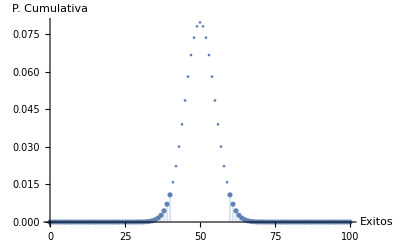

```mathematica
Show[
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,0,100},PlotRange->All, AxesLabel->{"Exitos", "P. Cumulativa"},Filling->None],
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,0,40},PlotRange->All, AxesLabel->{"Exitos", "P. Cumulativa"}],
DiscretePlot[PDF[BinomialDistribution[100,0.5],k],{k,60,100},PlotRange->All, AxesLabel->{"Exitos", "P. Cumulativa"}]
]
```

Se multiplica por dos la probabilidad cumulativa debido a la simetría de la gráfica anterior.

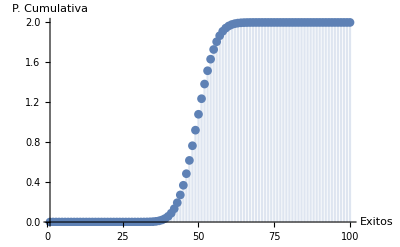

```mathematica
DiscretePlot[2*CDF[BinomialDistribution[100,0.5],k],{k,100},PlotRange->All,PlotMarkers->Automatic, AxesLabel->{"Exitos", "P. Cumulativa"}]
```

A partir de 40 éxitos la probabilidad cumulativa supera 0.05, de manera que se pueden rechazar los resultados que obtengan resultados menores a 40. De la misma manera (por simetría) se rechazan los resultados mayores a 60.

Una manera más simple de calcular el intervalo de confianza es utilizando los cuantiles de α/2 a 1-α/2.

```mathematica
Quantile[BinomialDistribution[100,0.5],{α/2,1-α/2}]
```

{40,60}